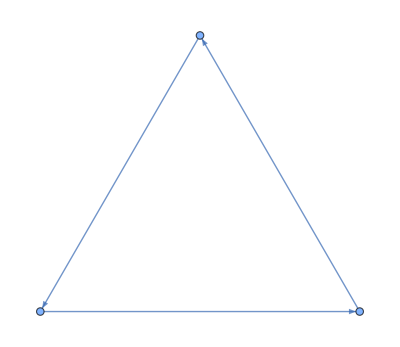

```mathematica
g=Graph[{1->2, 2->3, 3->1}]
```

```mathematica
EdgeList[g]
```

{1->2,2->3,3->1}

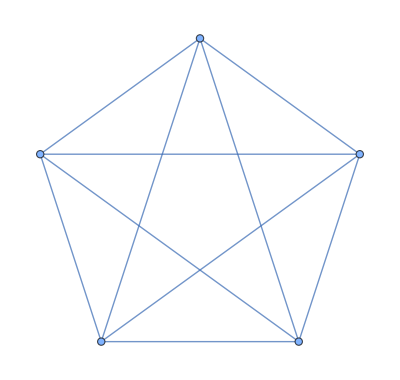

```mathematica
CompleteGraph[5]
```

all vertices are connected to all other vertices (K_n)

bipartite graph

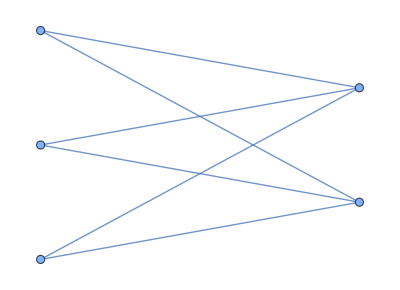

```mathematica
CompleteGraph[{3, 2}]
```

within those two sets ,there are no edges
complete bipartite - connected to other set

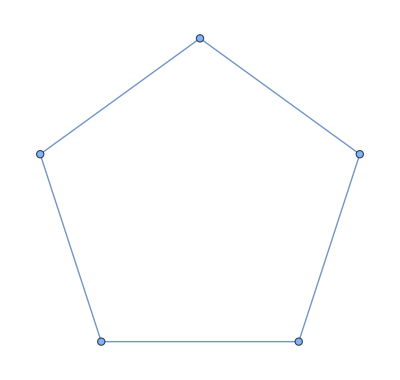

```mathematica
CycleGraph[5]
```

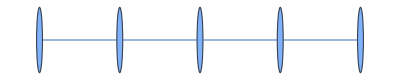

```mathematica
PathGraph[Range[5]]
```

degree = number of edges incident to that vertex
handshake lemma
sum of degrees of all vertices = 2x number of edges

proper coloring - any two adjacent vertices (conected by edge) receive different colors
chromatic number = smallest number of colors required for a proper coloring

cn of complete graph = # of v

cyclic: 2 if n even, 3 if n odd

brooks thm: odd cycles, complete graphs

at a party, there are 6 people. each pair of people are either friends or strangers.is it possible that there is no set of three people who are all friends or all strangers

for any n and m there exists some number r(n, m) such that any 2 coloring of K_r(n, m) contains either a red K_n or blue K_m